# Density-dependent selection in a finite population (7-30-18)

In this version we have a reflecting boundary at 0,0 only.
Add mutation 
Truncate dynamics so that probability of overshoot is <threshold

```mathematica
test={r0->0.2,γ0->5,s->0.95,σ->0.05,μ->0,β->1,tMax->500,Δt->5};
```

## Density-dependent selection

Constraints on r and K

We define a trade-off such that r[i]γ[i]^(1/β)=Constant

```mathematica
Solve[{r0 γ0^(1/β)==r[i] γ[i]^(1/β)},γ[i]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ[i]→((r0 γ0^(1/β))/r[i])^β}}

```mathematica
tOffSub=Join[{γ[1]-> γ0(r0/r[1])^β,γ[2]-> γ0(r0/r[2])^β}/.{r[1]->r0,r[2]->r0+σ},{r[1]->r0,r[2]->r0+σ}];
```

## Plots of trade-off Not done

Evolution in an infinite population

```mathematica
Clear[n]
```

```mathematica
n2[i_]:=n[i](1-μ)(1+r[i](1-(n[1]+n[2])/γ[i]))+μ n[Mod[i,2]+1](1+r[Mod[i,2]+1](1-(n[1]+n[2])/γ[Mod[i,2]+1]))
```

```mathematica
n2[1]
```

(1-μ) n[1] (1+r[1] (1-(n[1]+n[2])/γ[1]))+μ n[2] (1+r[2] (1-(n[1]+n[2])/γ[2]))

## Equilibria

```mathematica
equs={n2[1]==n[1],n2[2]==n[2]};
vars={n[1],n[2]};
```

```mathematica
equi=Simplify[Solve[equs,vars]/.tOffSub,Assumptions->{r0>0,γ0>0,β>0,σ>0}];
```

When mutation is absent the equilibria simplify to:

```mathematica
Solve[equs/.tOffSub/.{μ->0},vars]
```

{{n[1]→0,n[2]→0},{n[1]→γ0,n[2]→0},{n[1]→0,n[2]→γ0 (r0/(r0+σ))^β}}

## Numerical dynamics

```mathematica
nsol[pars_,n0_]:=Block[{out},out={n0};
For[t=1,t≤tMax/.pars,t++,
AppendTo[out,{n2[1],n2[2]}/.tOffSub/.pars/.{n[1]->out[[t,1]],n[2]->out[[t,2]]}]
];
out
]
```

ReplaceAll::reps: {test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

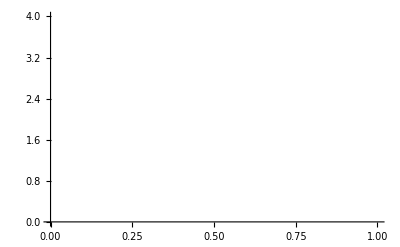

```mathematica
ListLinePlot[{nsol[test,{2,2}][[;;,1]],nsol[test,{2,2}][[;;,2]]}]
```

ReplaceAll::reps: {test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

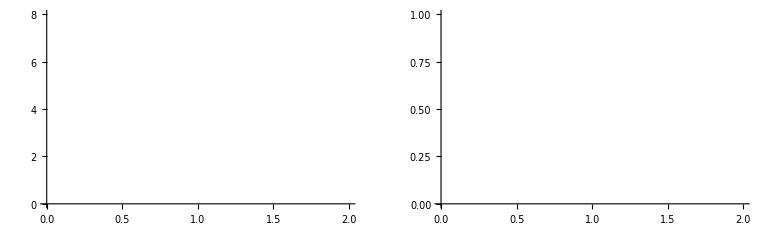

```mathematica
GraphicsRow[{ListLinePlot[nsol[test,{2,2}][[;;,1]]+nsol[test,{2,2}][[;;,2]],PlotRange->All],ListLinePlot[(nsol[test,{2,2}][[;;,1]])/(nsol[test,{2,2}][[;;,1]]+nsol[test,{2,2}][[;;,2]]),PlotRange->All]}]
```

Evolution in a finite population

## Transition Matrix

### Birth Matrix

```mathematica
Poi[λ_,x_]:=If[λ≤ 0,If[x==0,1,0],If[x≥0,(ⅇ^-λ λ^x)/(x!),0]]
```

```mathematica
subm[i1_,j1_,nMax_,pars_]:=Block[{out,i2,j2},out=Table[0,{j2,0,nMax},{i2,0,nMax}];
For[j2=0,j2≤ nMax,j2++,
For[i2=0,i2≤ nMax,i2++,
out[[j2+1,i2+1]]=Poi[i1 r[1](1-(i1+i2)/γ[1])/.tOffSub/.pars,j1-i1]Poi[i2 r[2](1-(i1+i2)/γ[2])/.tOffSub/.pars,j2-i2];
]
];
out
]
```

```mathematica
ConMtrx[nMax_,pars_]:=Block[{i1,j1,out,temp},out={};
For[j1=0,j1≤nMax,j1++,
temp={};
For[i1=0,i1≤ nMax,i1++,
temp=Join[temp,Transpose[subm[i1,j1,nMax,pars]]]
];
out=Join[out,Transpose[temp]];
];
out
]
```

```mathematica
e[i1_,i2_,nMax_]:=i1 *(nMax+1)+i2+1
```

This test calculates the probabilities of ending of with either nMax of type 1  or nMax of type 2.

```mathematica
testM[nMax_,pars_]:=Block[{temp,i1,i2,j,out,mtrx},mtrx=ConMtrx[nMax,pars];temp={};
For[i1=0,i1≤nMax,i1++,
For[i2=0,i2≤nMax,i2++,
For[j=i1,j≤nMax,j++,
If[i1==j&&i2==nMax,0,AppendTo[temp,mtrx[[e[j,nMax,nMax],e[i1,i2,nMax]]]]];
];
For[j=i2,j<nMax,j++,
If[i1==nMax&&i2==j,0,AppendTo[temp,mtrx[[e[nMax,j,nMax],e[i1,i2,nMax]]]]];
]
]
];
Max[temp]
]
```

```mathematica
Clear[BMtrx,bMtrx]
BMtrx[pars_,thresh_]:=BMtrx[pars,thresh]=Block[{out,temp,nMax},temp=1;nMax=1;
While[temp>thresh,
nMax++;
temp=testM[nMax,pars];
(*Print[{nMax,temp}]*)
];
out=ConMtrx[nMax,pars];
(*Normalizing*)
Transpose[Transpose[out]/Total[out]]
]
```

```mathematica
nMax[pars_,thresh_]:=Sqrt[Length[BMtrx[pars,thresh]]]-1
```

### Mutation Matrix

```mathematica
Pμ[i1_,i2_,j1_,j2_,pars_]:=Block[{x1,x2,out},out=0;(*out={};*)
If[i1+i2==j1+j2,
For[x2=0,x2≤i2,x2++,
x1=i1-j1+x2;
(*Print[{x1,x2,PDF[BinomialDistribution[i1,μ],x1]/.pars,PDF[BinomialDistribution[i2,μ],x2]/.pars}];*)
(*AppendTo[out,{x1,x2,PDF[BinomialDistribution[i1,μ],x1]PDF[BinomialDistribution[i2,μ],x2]/.pars}]*)
out+=PDF[BinomialDistribution[i1,μ],x1]PDF[BinomialDistribution[i2,μ],x2]/.pars;
]
];
out
]
```

```mathematica
Pμ2[i1_,i2_,j1_,j2_,pars_]:=Block[{x1,x2,out},out=0;out={};
If[i1+i2==j1+j2,
For[x2=0,x2≤i2,x2++,
x1=i1-j1+x2;
AppendTo[out,{x1->j1,x2->j2,PDF[BinomialDistribution[i1,μ],x1]PDF[BinomialDistribution[i2,μ],x2]/.pars}]
(*out+=PDF[BinomialDistribution[i1,μ],x1]PDF[BinomialDistribution[i2,μ],x2]/.pars;*)
]
];
out
]
```

```mathematica
Pμ[2,2,1,3,test]
```

ReplaceAll::reps: {test} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(0/.test)+(2 (1-μ)^3 μ/.test)+(2 (1-μ) μ^3/.test)

```mathematica
MuMtrx[pars_,nMax_]:=Block[{out,i1,i2,j1,j2},out=Table[0,{r,1,(nMax+1)^2},{c,1,(nMax+1)^2}];
For[i1=0,i1≤nMax,i1++,
For[i2=0,i2≤nMax,i2++,
For[j1=0,j1≤nMax,j1++,
For[j2=0,j2≤nMax,j2++,
out[[e[j1,j2,nMax],e[i1,i2,nMax]]]=Pμ[i1,i2,j1,j2,pars];
]
]
]
];
(*Normalizing as there could be more than nMax individuals of a particular type post mutation*)
Transpose[Transpose[out]/Total[out]]
]
```

### Survival Matrix

```mathematica
SMtrx[pars_,nMax_]:=Block[{out,i1,i2,j1,j2},out=Table[0,{r,1,(nMax+1)^2},{c,1,(nMax+1)^2}];
For[i1=0,i1≤nMax,i1++,
For[i2=0,i2≤nMax,i2++,
For[j1=0,j1≤nMax,j1++,
For[j2=0,j2≤nMax,j2++,
out[[e[j1,j2,nMax],e[i1,i2,nMax]]]=PDF[BinomialDistribution[i1,s],j1]PDF[BinomialDistribution[i2,s],j2]/.pars
]
]
]
];
out//Chop
]
```

### Transition Matrix

```mathematica
nm=nMax[test,0.001];
```

```mathematica
Clear[TMtrx]
TMtrx[pars_,thresh_]:=TMtrx[pars,thresh]=Block[{out,temp,i1,i2,nm},nm=nMax[pars,thresh];
out=SMtrx[pars,nm].MuMtrx[pars,nm].BMtrx[pars,thresh];
For[i1=0,i1≤nm,i1++,
For[i2=0,i2≤nm,i2++,
out[[e[0,0,nm],e[i1,i2,nm]]]=0;
]
];
out[[e[1,0,nm],e[0,0,nm]]]=0.5;out[[e[0,1,nm],e[0,0,nm]]]=0.5;
out=Transpose[Transpose[out]/Total[out]]
]
```

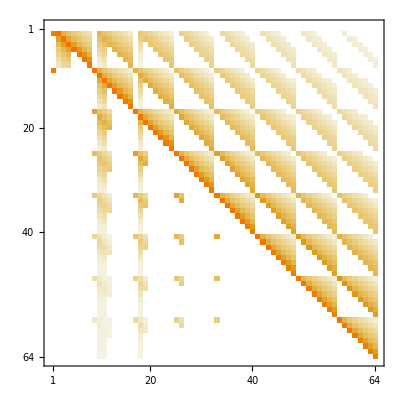

```mathematica
TMtrx[test,0.001]//MatrixPlot
```

## Dynamics

### Initial vector

```mathematica
vec0[pars_,thresh_,n0_]:=Block[{out,i1,i2},out={};
For[i1=0,i1≤nMax[pars,thresh],i1++,
For[i2=0,i2≤ nMax[pars,thresh],i2++,
If[i1==n0[[1]]&&i2==n0[[2]],AppendTo[out,1],AppendTo[out,0]];
]
];
out//N
]
```

### vector to matrix

```mathematica
v2m[pars_,thresh_,vIn_]:=Block[{out2,i1,i2,ct},out2=Table[0,{i1,0,nMax[pars,thresh]},{i2,0,nMax[pars,thresh]}];ct=1;
For[i1=0,i1≤nMax[pars,thresh],i1++,
For[i2=0,i2≤nMax[pars,thresh],i2++,
out2[[i1+1,i2+1]]=vIn[[ct]];
ct++;
];
];
out2
]
```

### Stochastic simulation

```mathematica
sim[pars_,thresh_,n0_]:=Block[{out,j1,j2,t,temp,jVec},out={n0};jVec={};
For[j1=0,j1≤nMax[pars,thresh],j1++,
For[j2=0,j2≤nMax[pars,thresh],j2++,
AppendTo[jVec,{j1,j2}]
]
];
For[t=1,t≤tMax/.pars,t++,
temp=TMtrx[pars,thresh][[;;,e[out[[t,1]],out[[t,2]],nMax[pars,thresh]]]];
AppendTo[out,RandomChoice[temp->jVec]];
];
out
]
```

### Examples

```mathematica
test1={r0->0.2,γ0->4,s->0.95,σ->0.1,μ->0,β->2,tMax->500,Δt->5};
```

```mathematica
equi/.test1
```

{{n[1]→0,n[2]→0},{n[1]→4.,n[2]→-2.14163×10^-16},{n[1]→0.,n[2]→1.77778}}

```mathematica
{statDist[test1,0.01,2][[1]]//Total,statDist[test1,0.01,2][[;;,1]]//Total}
```

{-0.614043,1.78514}

```mathematica
sim1=sim[test1,0.01,{2,2}];
```

```mathematica
test2={r0->0.2,γ0->8,s->0.95,σ->0.1,μ->0,β->2,tMax->500,Δt->5};
```

```mathematica
equi/.test2
```

{{n[1]→0,n[2]→0},{n[1]→8.,n[2]→-4.28327×10^-16},{n[1]→0.,n[2]→3.55556}}

```mathematica
sim2=sim[test2,0.01,{4,4}];
```

```mathematica
test3={r0->0.2,γ0->20,s->0.95,σ->0.1,μ->0,β->0.5,tMax->500,Δt->5};
```

```mathematica
equi/.test3
```

{{n[1]→0,n[2]→0},{n[1]→20.,n[2]→-1.5658×10^-14},{n[1]→-2.36334×10^-14,n[2]→16.3299}}

```mathematica
sim3=sim[test2,0.01,{10,10}];
```

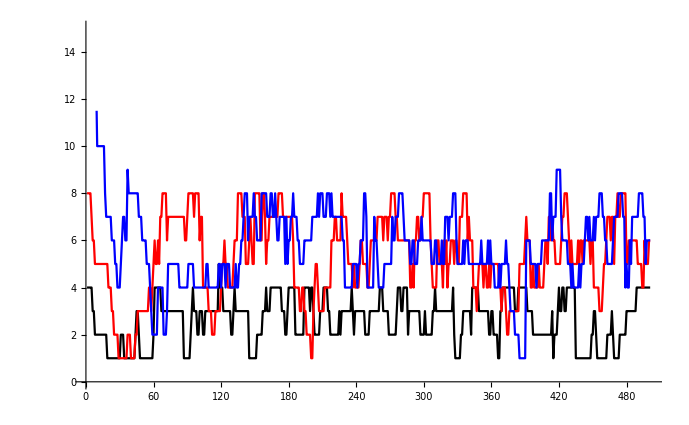

```mathematica
Show[{ListLinePlot[sim1[[;;,1]]+sim1[[;;,2]],PlotStyle->Black],ListLinePlot[sim2[[;;,1]]+sim2[[;;,2]],PlotStyle->Red],ListLinePlot[sim3[[;;,1]]+sim3[[;;,2]],PlotStyle->Blue]},PlotRange->{0,15}]
```

```mathematica
TMtrx[test1,0.001]//Total
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

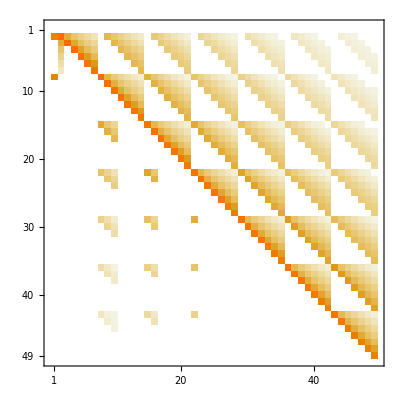

```mathematica
TMtrx[test1,0.001]//MatrixPlot
```

## Stationary Distribution

```mathematica
Clear[equs,vars]
```

```mathematica
vars[pars_,thresh_]:=Table[Π[i1,i2],{i1,0,nMax[pars,thresh]},{i2,0,nMax[pars,thresh]}]//Flatten
```

```mathematica
equs[pars_,thresh_]:=Join[Table[(TMtrx[pars,thresh].vars[pars,thresh])[[j]]==vars[pars,thresh][[j]],{j,2,Length[vars[pars,thresh]]}],{Total[vars[pars,thresh]]==1}]
```

```mathematica
esys[pars_,thresh_]:=Eigensystem[TMtrx[pars,thresh]]//Chop
```

```mathematica
esys[test,0.001]
```

{{1.,1.,0.955751,0.907999,0.899226,0.875491,0.834737,0.789621,0.773781,0.770665,0.748569+0.0190477 ⅈ,0.748569-0.0190477 ⅈ,0.740318+0.0106442 ⅈ,0.740318-0.0106442 ⅈ,0.735092,0.735092,0.727557,0.717212+0.00938604 ⅈ,0.717212-0.00938604 ⅈ,0.711053+0.00539985 ⅈ,0.711053-0.00539985 ⅈ,0.708033,0.702774,0.700837,0.698337,0.698337,0.698337,0.69724,0.694951,0.684458,0.663645,0.663479+0.0000706272 ⅈ,0.663479-0.0000706272 ⅈ,0.66342,0.66342,0.66342,0.66342,0.63369,0.63025,0.630249,0.630249,0.630249,0.630238,0.630237,0.608312,0.598738,0.598737,0.598737,0.598737,0.598736,0.5688,0.5688,0.5688,0.5688,0.548318,0.54655,0.54036,0.54036,0.54036,0.513342,0.513342,0.499067,0.487675,0},{{0,0.174816,0.333317,0.506566,0.423951,0.0296417,0.00147518,0.0000549926,-0.140948+0.0398546 ⅈ,0,0,0,0,0,0,0,-0.231746+0.0655286 ⅈ,0,0,0,0,0,0,0,-0.346895+0.0980882 ⅈ,0,0,0,0,0,0,0,-0.380737+0.107657 ⅈ,0,0,0,0,0,0,0,-0.225538+0.0637731 ⅈ,0,0,0,0,0,0,0,-0.0141777+0.0040089 ⅈ,0,0,0,0,0,0,0,-0.000602895+0.000170475 ⅈ,0,0,0,0,0,0,0},{0,0.174816,0.333317,0.506566,0.423951,0.0296417,0.00147518,0.0000549926,-0.140948-0.0398546 ⅈ,0,0,0,0,0,0,0,-0.231746-0.0655286 ⅈ,0,0,0,0,0,0,0,-0.346895-0.0980882 ⅈ,0,0,0,0,0,0,0,-0.380737-0.107657 ⅈ,0,0,0,0,0,0,0,-0.225538-0.0637731 ⅈ,0,0,0,0,0,0,0,-0.0141777-0.0040089 ⅈ,0,0,0,0,0,0,0,-0.000602895-0.000170475 ⅈ,0,0,0,0,0,0,0},{0,-0.00417721,0.0961754,0.261793,0.27823,0.0184486,0.000884765,0.0000319584,-0.00195097,-0.20414,-0.240381,-0.150971,-0.00731877,-0.000232787,-5.82882×10^-6,-1.17731×10^-7,0.0996312,-0.324258,-0.231784,-0.0371565,-0.000495013,-0.0000156084,-3.94405×10^-7,-8.08648×10^-9,0.294436,-0.345894,-0.0914045,-0.000992976,-0.0000199628,-5.75023×10^-7,-1.40827×10^-8,-2.87292×10^-10,0.448666,-0.184095,-0.00316303,-0.0000299232,-6.68763×10^-7,-1.61799×10^-8,-3.61535×10^-10,0,0.318789,-0.00835713,-0.000083769,-9.84965×10^-7,-2.07516×10^-8,-4.10019×10^-10,0,0,0.0193256,-0.000268711,-1.91855×10^-6,-3.00466×10^-8,-5.93557×10^-10,0,0,0,0.000795099,-6.54516×10^-6,-3.94219×10^-8,-7.76408×10^-10,0,0,0,0},{0,0,0,0,0,0,0,0,0.621944,0,0,0,0,0,0,0,0.402661,0,0,0,0,0,0,0,-0.0537041,0,0,0,0,0,0,0,-0.497523,0,0,0,0,0,0,0,-0.447215,0,0,0,0,0,0,0,-0.025186,0,0,0,0,0,0,0,-0.000976434,0,0,0,0,0,0,0},{0,0.002674,-0.0017884,-0.10214,-0.173981,-0.0100666,-0.00044572,-0.0000151585,0.0030328,0.00795822,0.291741,0.296827,0.0126734,0.000374997,8.96337×10^-6,1.74762×10^-7,-0.00231347,-0.277067,0.187972,0.0847067,0.000672227,0.0000223174,5.66812×10^-7,1.15003×10^-8,0.0866707,-0.577207,0.0807079,0.00115729,0.0000165856,6.65591×10^-7,1.82354×10^-8,3.85444×10^-10,0.261289,-0.429112,0.00181139,-4.69392×10^-7,1.26844×10^-7,1.17483×10^-8,3.80604×10^-10,0,0.257506,-0.018131,0.000019207,-6.40096×10^-7,-7.33049×10^-9,0,0,0,0.0144345,-0.000555131,-2.53435×10^-7,-2.64146×10^-8,-4.05392×10^-10,0,0,0,0.000558065,-0.0000129964,-1.74609×10^-8,-7.3699×10^-10,0,0,0,0},{0,-0.625371,-0.342668,0.304019,0.630913,0.0317502,0.00131415,0.0000424644,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.000370575,0.00257775,0.0108043,0.090481,0.00237719,0.0000820178,2.43876×10^-6,-0.0000121644,-0.00510165,-0.026297,-0.350018,-0.00249861,-0.0000576228,-1.21613×10^-6,-2.1886×10^-8,0.00254866,0.0190183,0.499949,-0.177879,-0.000105287,-3.05283×10^-6,-7.16849×10^-8,-1.37625×10^-9,-0.00393637,-0.314306,0.498089,-0.00205015,-2.4566×10^-6,-8.65499×10^-8,-2.21894×10^-9,0,0.0735941,-0.462048,0.0114104,-0.0000177914,-2.75212×10^-8,-1.56322×10^-9,0,0,0.142365,-0.0156722,0.000210887,-7.63507×10^-8,4.13627×10^-10,0,0,0,0.00634494,-0.000427714,3.22359×10^-6,1.489×10^-9,0,0,0,0,0.000214089,-9.25433×10^-6,4.14122×10^-8,0,0,0,0,0},{0,-0.125481,-0.170658,-0.00210343,0.23287,-0.0227176,-0.000360714,-8.95272×10^-6,0.0475365,0.468406,0.136905,-0.224091,0.0643882,0.000632418,0.0000104555,1.66079×10^-7,-0.271674,0.301524,-0.0176166,-0.312064,0.00147944,0.0000297192,5.88774×10^-7,1.02468×10^-8,-0.316057,-0.0767788,0.114283,-0.000135998,0.0000445221,9.53251×10^-7,1.93704×10^-8,3.46087×10^-10,0.0962559,-0.290736,0.00263269,0.0000509492,1.339×10^-6,2.58934×10^-8,4.89862×10^-10,0,0.361215,-0.00469246,0.0000815137,1.99084×10^-6,3.89688×10^-8,6.5933×10^-10,0,0,0.00677422,-0.000103173,2.26294×10^-6,5.76162×10^-8,1.04844×10^-9,0,0,0,0.000153679,-1.94163×10^-6,5.23576×10^-8,1.363×10^-9,0,0,0,0},{0,0,0,0,0,0.0629941,0,0,0,0,0,0,-0.31497,0,0,0,0,0,0,0.629941,0,0,0,0,0,0,-0.629941,0,0,0,0,0,0,0.31497,0,0,0,0,0,0,-0.0629941,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.393803,0,0,0,0,0,0,0,-0.413758,0,0,0,0,0,0,0,-0.612472,0,0,0,0,0,0,0,0.0976757,0,0,0,0,0,0,0,0.537637,0,0,0,0,0,0,0,-0.00277001,0,0,0,0,0,0,0,-0.000115308,0,0,0,0,0,0,0},{0,0.391706-0.019942 ⅈ,-0.40819+0.123494 ⅈ,-0.630147,0.293003-0.201904 ⅈ,0.366088+0.0774551 ⅈ,-0.0121044+0.020752 ⅈ,-0.000354684+0.000145384 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.391706+0.019942 ⅈ,-0.40819-0.123494 ⅈ,-0.630147,0.293003+0.201904 ⅈ,0.366088-0.0774551 ⅈ,-0.0121044-0.020752 ⅈ,-0.000354684-0.000145384 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-0.0688445-0.128843 ⅈ,0.0157401+0.142471 ⅈ,0.199931+0.187451 ⅈ,0.0795248-0.0932727 ⅈ,-0.174078-0.0849048 ⅈ,0.0194229-0.0072783 ⅈ,0.000169647+0.000105184 ⅈ,-0.0334001+0.00176037 ⅈ,0.167555-0.00335572 ⅈ,-0.373499+0.0220091 ⅈ,-0.320807-0.0515897 ⅈ,0.0957198-0.0470962 ⅈ,-0.00264044+0.00763238 ⅈ,-0.0000547639+0.0000185406 ⅈ,-6.78316×10^-7+1.38295×10^-7 ⅈ,-0.0348645-0.00589646 ⅈ,0.430463,0.140556+0.0436375 ⅈ,0.37339+0.0528085 ⅈ,-0.00448993+0.0130146 ⅈ,-0.000133345+0.0000453281 ⅈ,-2.22403×10^-6+4.63908×10^-7 ⅈ,-3.53447×10^-8+5.6306×10^-9 ⅈ,-0.11386-0.00635608 ⅈ,-0.0422112+0.0113208 ⅈ,-0.384391-0.0546968 ⅈ,-0.00881591+0.0137094 ⅈ,-0.0000877603+0.0000323936 ⅈ,-2.50721×10^-6+5.43615×10^-7 ⅈ,-5.58354×10^-8+9.20921×10^-9 ⅈ,-1.01843×10^-9+1.40355×10^-10 ⅈ,0.00584664-0.00665545 ⅈ,-0.103229+0.0265223 ⅈ,0.0280951-0.0413797 ⅈ,0.0000504206-0.0000202829 ⅈ,-6.66611×10^-8+1.20327×10^-7 ⅈ,-3.16408×10^-8+6.22357×10^-9 ⅈ,-9.70866×10^-10+1.44563×10^-10 ⅈ,0,0.114544-0.00132748 ⅈ,0.00504829+0.00134131 ⅈ,0.000458181-0.0000618787 ⅈ,3.51837×10^-6-5.32385×10^-7 ⅈ,3.65263×10^-8-2.28904×10^-9 ⅈ,0,0,0,-0.0109591+0.00883789 ⅈ,4.63367×10^-6+0.0000510443 ⅈ,7.49795×10^-6-4.70927×10^-7 ⅈ,1.06156×10^-7-1.06621×10^-8 ⅈ,1.46649×10^-9,0,0,0,-0.000161257-0.000034845 ⅈ,4.56137×10^-8+7.37454×10^-7 ⅈ,1.29814×10^-7-6.38479×10^-9 ⅈ,2.46796×10^-9-1.85516×10^-10 ⅈ,0,0,0,0},{0,-0.0688445+0.128843 ⅈ,0.0157401-0.142471 ⅈ,0.199931-0.187451 ⅈ,0.0795248+0.0932727 ⅈ,-0.174078+0.0849048 ⅈ,0.0194229+0.0072783 ⅈ,0.000169647-0.000105184 ⅈ,-0.0334001-0.00176037 ⅈ,0.167555+0.00335572 ⅈ,-0.373499-0.0220091 ⅈ,-0.320807+0.0515897 ⅈ,0.0957198+0.0470962 ⅈ,-0.00264044-0.00763238 ⅈ,-0.0000547639-0.0000185406 ⅈ,-6.78316×10^-7-1.38295×10^-7 ⅈ,-0.0348645+0.00589646 ⅈ,0.430463,0.140556-0.0436375 ⅈ,0.37339-0.0528085 ⅈ,-0.00448993-0.0130146 ⅈ,-0.000133345-0.0000453281 ⅈ,-2.22403×10^-6-4.63908×10^-7 ⅈ,-3.53447×10^-8-5.6306×10^-9 ⅈ,-0.11386+0.00635608 ⅈ,-0.0422112-0.0113208 ⅈ,-0.384391+0.0546968 ⅈ,-0.00881591-0.0137094 ⅈ,-0.0000877603-0.0000323936 ⅈ,-2.50721×10^-6-5.43615×10^-7 ⅈ,-5.58354×10^-8-9.20921×10^-9 ⅈ,-1.01843×10^-9-1.40355×10^-10 ⅈ,0.00584664+0.00665545 ⅈ,-0.103229-0.0265223 ⅈ,0.0280951+0.0413797 ⅈ,0.0000504206+0.0000202829 ⅈ,-6.66611×10^-8-1.20327×10^-7 ⅈ,-3.16408×10^-8-6.22357×10^-9 ⅈ,-9.70866×10^-10-1.44563×10^-10 ⅈ,0,0.114544+0.00132748 ⅈ,0.00504829-0.00134131 ⅈ,0.000458181+0.0000618787 ⅈ,3.51837×10^-6+5.32385×10^-7 ⅈ,3.65263×10^-8+2.28904×10^-9 ⅈ,0,0,0,-0.0109591-0.00883789 ⅈ,4.63367×10^-6-0.0000510443 ⅈ,7.49795×10^-6+4.70927×10^-7 ⅈ,1.06156×10^-7+1.06621×10^-8 ⅈ,1.46649×10^-9,0,0,0,-0.000161257+0.000034845 ⅈ,4.56137×10^-8-7.37454×10^-7 ⅈ,1.29814×10^-7+6.38479×10^-9 ⅈ,2.46796×10^-9+1.85516×10^-10 ⅈ,0,0,0,0},{0,0,3.54783×10^-10,0,-4.70946×10^-10,0.0586828,-0.0212917,0,2.55865×10^-10,-6.92462×10^-10,4.53282×10^-10,3.77799×10^-10,-0.293414,0.069067,0,0,0,-6.29199×10^-10,3.47759×10^-10,0.586828,-0.0259595,0,0,0,0,0,-0.586828,-0.160998,0,0,0,0,0,0.293414,0.267456,0,0,0,0,0,-0.0586828,-0.165666,0,0,0,0,0,0,0.0373915,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-0.0210455,-0.0203218,0,0,0,0,0,0.105227,0.142977,0,0,0,0,0,-0.210455,-0.410055,0,0,0,0,0,0.210455,0.616892,0,0,0,0,0,-0.105227,-0.515283,0,0,0,0,0,0.0210455,0.227159,0,0,0,0,0,0,-0.0413674,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.041263,-0.284256,-0.0720621,0.273336,-0.0441359,0.0141169,-0.000116741,-0.191225,0.455871,-0.0480494,0.0766696,-0.00356808,0.00130172,-8.75059×10^-6,-8.78336×10^-8,0.0877613,0.116338,-0.629588,-0.0259839,0.000807317,-0.0000145341,-2.30743×10^-7,-3.73049×10^-9,0.17738,0.136472,0.121685,-0.0113036,0.0000142141,-5.30082×10^-8,-3.45111×10^-9,0,-0.0769537,-0.142931,0.200806,0.0000983112,6.58454×10^-7,5.16281×10^-9,0,0,-0.12865,-0.109713,-0.00114464,1.7183×10^-6,2.17722×10^-8,2.50607×10^-10,0,0,0.0653829,0.000979164,-8.74574×10^-6,3.86013×10^-8,5.93554×10^-10,0,0,0,-0.000582803,0.0000115936,-6.77903×10^-8,8.02243×10^-10,0,0,0,0},{0,-0.0859164+0.0761728 ⅈ,0.179601-0.09844 ⅈ,0.162861-0.103046 ⅈ,-0.264632+0.10304 ⅈ,0.00228787+0.0139761 ⅈ,-0.0108029+0.00254375 ⅈ,0.000165575-0.000267708 ⅈ,0.0585866-0.0352456 ⅈ,-0.121995-0.0543667 ⅈ,-0.123841+0.0570997 ⅈ,0.344494+0.0346336 ⅈ,-0.000894148-0.00368366 ⅈ,0.00222522-0.000280178 ⅈ,-0.0000289547+0.0000370794 ⅈ,-3.07354×10^-7+2.08404×10^-7 ⅈ,-0.0395773+0.0983782 ⅈ,0.130381-0.0736218 ⅈ,-0.418559,-0.156466-0.037392 ⅈ,0.00391377-0.000314324 ⅈ,-0.0000740035+0.0000910355 ⅈ,-1.04272×10^-6+6.95455×10^-7 ⅈ,-1.48863×10^-8+8.50971×10^-9 ⅈ,-0.115806+0.0579607 ⅈ,0.404721+0.0341818 ⅈ,0.309521+0.00661518 ⅈ,-0.00839079-0.00502531 ⅈ,-0.0000603706+0.0000627166 ⅈ,-1.26665×10^-6+7.81252×10^-7 ⅈ,-2.46918×10^-8+1.35165×10^-8 ⅈ,-4.19998×10^-10+2.17359×10^-10 ⅈ,-0.0907758-0.110304 ⅈ,-0.268+0.0696389 ⅈ,0.0452088+0.0225107 ⅈ,0.000140556-0.000109178 ⅈ,-2.96821×10^-7-3.97829×10^-9 ⅈ,-1.67601×10^-8+7.27933×10^-9 ⅈ,-4.35867×10^-10+2.04111×10^-10 ⅈ,0,0.145332-0.0797424 ⅈ,-0.123284-0.0538108 ⅈ,-0.000946207+0.000366357 ⅈ,1.77231×10^-6-1.29299×10^-6 ⅈ,9.16833×10^-9-1.01597×10^-8 ⅈ,-1.03013×10^-10,0,0,0.0396644+0.0807188 ⅈ,0.0036485-0.00160409 ⅈ,-6.15435×10^-6-3.24337×10^-7 ⅈ,3.90569×10^-8-2.84734×10^-8 ⅈ,4.48512×10^-10-3.54516×10^-10 ⅈ,0,0,0,-0.00273317-0.000770116 ⅈ,0.0000385914-4.16956×10^-6 ⅈ,-3.68463×10^-8-2.0131×10^-8 ⅈ,8.40632×10^-10-5.81084×10^-10 ⅈ,0,0,0,0},{0,-0.0859164-0.0761728 ⅈ,0.179601+0.09844 ⅈ,0.162861+0.103046 ⅈ,-0.264632-0.10304 ⅈ,0.00228787-0.0139761 ⅈ,-0.0108029-0.00254375 ⅈ,0.000165575+0.000267708 ⅈ,0.0585866+0.0352456 ⅈ,-0.121995+0.0543667 ⅈ,-0.123841-0.0570997 ⅈ,0.344494-0.0346336 ⅈ,-0.000894148+0.00368366 ⅈ,0.00222522+0.000280178 ⅈ,-0.0000289547-0.0000370794 ⅈ,-3.07354×10^-7-2.08404×10^-7 ⅈ,-0.0395773-0.0983782 ⅈ,0.130381+0.0736218 ⅈ,-0.418559,-0.156466+0.037392 ⅈ,0.00391377+0.000314324 ⅈ,-0.0000740035-0.0000910355 ⅈ,-1.04272×10^-6-6.95455×10^-7 ⅈ,-1.48863×10^-8-8.50971×10^-9 ⅈ,-0.115806-0.0579607 ⅈ,0.404721-0.0341818 ⅈ,0.309521-0.00661518 ⅈ,-0.00839079+0.00502531 ⅈ,-0.0000603706-0.0000627166 ⅈ,-1.26665×10^-6-7.81252×10^-7 ⅈ,-2.46918×10^-8-1.35165×10^-8 ⅈ,-4.19998×10^-10-2.17359×10^-10 ⅈ,-0.0907758+0.110304 ⅈ,-0.268-0.0696389 ⅈ,0.0452088-0.0225107 ⅈ,0.000140556+0.000109178 ⅈ,-2.96821×10^-7+3.97829×10^-9 ⅈ,-1.67601×10^-8-7.27933×10^-9 ⅈ,-4.35867×10^-10-2.04111×10^-10 ⅈ,0,0.145332+0.0797424 ⅈ,-0.123284+0.0538108 ⅈ,-0.000946207-0.000366357 ⅈ,1.77231×10^-6+1.29299×10^-6 ⅈ,9.16833×10^-9+1.01597×10^-8 ⅈ,-1.03013×10^-10,0,0,0.0396644-0.0807188 ⅈ,0.0036485+0.00160409 ⅈ,-6.15435×10^-6+3.24337×10^-7 ⅈ,3.90569×10^-8+2.84734×10^-8 ⅈ,4.48512×10^-10+3.54516×10^-10 ⅈ,0,0,0,-0.00273317+0.000770116 ⅈ,0.0000385914+4.16956×10^-6 ⅈ,-3.68463×10^-8+2.0131×10^-8 ⅈ,8.40632×10^-10+5.81084×10^-10 ⅈ,0,0,0,0},{0,2.40776×10^-9+2.27656×10^-9 ⅈ,-2.94943×10^-9-4.49241×10^-9 ⅈ,-2.81304×10^-9-2.93456×10^-9 ⅈ,3.63781×10^-9+4.73484×10^-9 ⅈ,0,1.50665×10^-10+1.82374×10^-10 ⅈ,0,-0.298026-0.0225059 ⅈ,-2.09652×10^-9+2.12794×10^-9 ⅈ,2.00422×10^-10,-1.54802×10^-9-2.07488×10^-10 ⅈ,1.47925×10^-10,0,0,0,0.563866+0.0189357 ⅈ,-2.06478×10^-10-3.91653×10^-10 ⅈ,4.68035×10^-9-2.00891×10^-9 ⅈ,1.08634×10^-9,0,0,0,0,0.282535+0.0507946 ⅈ,-1.69362×10^-9-2.31×10^-10 ⅈ,-2.61588×10^-9+9.62253×10^-10 ⅈ,0,0,0,0,0,-0.566623,1.64513×10^-9-2.71706×10^-10 ⅈ,-6.42273×10^-10+2.23432×10^-10 ⅈ,0,0,0,0,0,-0.288118-0.0568924 ⅈ,4.69548×10^-10+1.62528×10^-10 ⅈ,0,0,0,0,0,0,0.320027+0.00355829 ⅈ,0,0,0,0,0,0,0,-0.0136598+0.00610975 ⅈ,0,0,0,0,0,0,0},{0,2.40776×10^-9-2.27656×10^-9 ⅈ,-2.94943×10^-9+4.49241×10^-9 ⅈ,-2.81304×10^-9+2.93456×10^-9 ⅈ,3.63781×10^-9-4.73484×10^-9 ⅈ,0,1.50665×10^-10-1.82374×10^-10 ⅈ,0,-0.298026+0.0225059 ⅈ,-2.09652×10^-9-2.12794×10^-9 ⅈ,2.00422×10^-10,-1.54802×10^-9+2.07488×10^-10 ⅈ,1.47925×10^-10,0,0,0,0.563866-0.0189357 ⅈ,-2.06478×10^-10+3.91653×10^-10 ⅈ,4.68035×10^-9+2.00891×10^-9 ⅈ,1.08634×10^-9,0,0,0,0,0.282535-0.0507946 ⅈ,-1.69362×10^-9+2.31×10^-10 ⅈ,-2.61588×10^-9-9.62253×10^-10 ⅈ,0,0,0,0,0,-0.566623,1.64513×10^-9+2.71706×10^-10 ⅈ,-6.42273×10^-10-2.23432×10^-10 ⅈ,0,0,0,0,0,-0.288118+0.0568924 ⅈ,4.69548×10^-10-1.62528×10^-10 ⅈ,0,0,0,0,0,0,0.320027-0.00355829 ⅈ,0,0,0,0,0,0,0,-0.0136598-0.00610975 ⅈ,0,0,0,0,0,0,0},{0,-0.350025,0.571104,0.412704,-0.616607,0.00820232,-0.0269086,0.00152919,3.41404×10^-9,-4.44248×10^-9,2.36321×10^-10,-1.29187×10^-9,1.5111×10^-10,0,0,0,-4.37541×10^-9,2.66964×10^-10,6.87891×10^-9,9.91659×10^-10,0,0,0,0,-3.38705×10^-9,-1.45561×10^-9,-3.64507×10^-9,-1.11216×10^-10,0,0,0,0,4.59124×10^-9,1.85674×10^-9,-9.34617×10^-10,0,0,0,0,0,2.76936×10^-9,3.55714×10^-10,0,0,0,0,0,0,-2.71823×10^-9,0,0,0,0,0,0,0,1.63605×10^-10,0,0,0,0,0,0,0},{0,0.351916,-0.553694,-0.394241,0.614086,-0.0375569,0.0353696,-0.0031995,0.0360523,-0.0947769,0.0116151,-0.0117443,0.000434818,-0.00023757,0.0000160485,3.63895×10^-8,-0.0251262,0.00588835,0.122157,0.00504563,-0.000327192,0.0000326039,1.05564×10^-7,1.31004×10^-9,-0.0379332,-0.0144887,-0.0605782,0.000125832,0.0000197914,9.49591×10^-8,1.68998×10^-9,0,0.0260426,0.0293995,-0.018031,-7.75358×10^-6,3.62103×10^-8,7.98101×10^-10,0,0,0.0263952,0.00229776,0.00171419,4.5241×10^-8,4.72254×10^-10,0,0,0,-0.0177597,-0.000608018,3.54513×10^-6,1.48904×10^-9,0,0,0,0,0.00169993,-1.7534×10^-6,2.87452×10^-8,0,0,0,0,0},{0,-0.334951,0.581744,0.356761,-0.642638,0.0821692,-0.0483691,0.00528305,-7.19192×10^-9,2.29998×10^-8,-5.01994×10^-9,2.37538×10^-9,2.59889×10^-10,0,0,0,3.1774×10^-9,1.77846×10^-10,-2.87267×10^-8,8.57547×10^-10,-1.98654×10^-10,0,0,0,7.34854×10^-9,3.00744×10^-9,1.31474×10^-8,-7.47566×10^-10,0,0,0,0,-3.32913×10^-9,-7.41123×10^-9,5.09552×10^-9,0,0,0,0,0,-4.63148×10^-9,-5.09206×10^-10,-6.68256×10^-10,0,0,0,0,0,2.54671×10^-9,2.36948×10^-10,0,0,0,0,0,0,-3.07206×10^-10,0,0,0,0,0,0,0},{0,0,-1.84793×10^-10,0,1.93238×10^-10,-0.0201711,0.0443772,-0.00847067,0,2.1456×10^-10,-2.35468×10^-10,0,0.100855,-0.225921,0.0149175,0,0,1.84504×10^-10,-1.85381×10^-10,-0.201711,0.463947,0.0682081,0,0,0,0,0.201711,-0.484121,-0.268329,0,0,0,0,-0.100855,0.262235,0.38936,0,0,0,0,0.0201711,-0.0645518,-0.286063,0,0,0,0,0,0.00403491,0.106113,0,0,0,0,0,0,-0.0157354,0,0,0,0,0,0,0},{0,0,-1.04315×10^-10,0,1.11051×10^-10,-0.0103466,0.0408363,-0.014476,0,0,-2.50893×10^-10,0,0.0517329,-0.224325,0.0604958,0,0,2.36263×10^-10,0,-0.103466,0.509078,-0.0693251,0,0,0,0,0.103466,-0.609794,-0.0541509,0,0,0,0,-0.0517329,0.405612,0.206599,0,0,0,0,0.0103466,-0.141552,-0.205082,0,0,0,0,0,0.0201431,0.0919526,0,0,0,0,0,0,-0.0160137,0,0,0,0,0,0,0},{0,1.96403×10^-9,-1.2515×10^-8,3.43052×10^-9,1.21919×10^-8,-0.0468704,0.0310055,-0.00596208,-4.52184×10^-9,1.80172×10^-8,-1.29077×10^-8,2.35589×10^-9,0.234352,-0.0922922,0.010729,0,3.92169×10^-10,8.56925×10^-9,-2.22958×10^-8,-0.468704,-0.00362226,0.013959,0,0,2.05301×10^-9,2.53526×10^-9,0.468704,0.3173,-0.0220576,0,0,0,-8.42055×10^-10,-0.234352,-0.472328,-0.0572674,0,0,0,0,0.0468704,0.282672,0.128826,0,0,0,0,0,-0.0627355,-0.090054,0,0,0,0,0,0,0.0218271,0,0,0,0,0,0,0},{0,-0.079218,0.0799986,0.269747,-0.127086,-0.147998,0.0425319,-0.00756955,-0.0236117,0.123256,-0.549689,0.0420823,0.19406,-0.0393422,0.00399199,-2.41574×10^-6,-0.0121162,0.522062,-0.140461,0.151389,-0.06277,0.00975996,-8.16305×10^-6,-8.84598×10^-8,-0.146803,0.0222571,-0.0223778,-0.00522456,0.00704075,-9.5022×10^-6,-1.43817×10^-7,-2.22062×10^-9,-0.00703104,-0.350102,0.0540362,-0.00563983,-1.56027×10^-6,-9.06454×10^-8,-2.21487×10^-9,0,0.189263,0.0885716,-0.0072982,0.0000109603,6.26625×10^-8,-3.76498×10^-10,0,0,-0.0639389,-0.0142203,0.0000115922,2.19078×10^-7,2.47284×10^-9,0,0,0,0.0124385,0.000010924,1.87472×10^-7,4.32412×10^-9,0,0,0,0},{0,0.0601593,-0.0485904,-0.173322,0.140551,0.0412058,-0.00633144,0.00157274,0.0251807,-0.121928,0.319826,-0.270251,-0.0433296,0.00605037,-0.000764853,1.50658×10^-6,0.00731288,-0.286715,0.503935,0.0598986,0.00946296,-0.00186515,5.09098×10^-6,5.30882×10^-8,0.0667723,-0.257562,-0.357376,0.00256238,-0.00135358,5.92252×10^-6,8.62176×10^-8,1.31477×10^-9,0.0632071,0.428234,0.00127426,0.00155806,1.06545×10^-6,5.46845×10^-8,1.31073×10^-9,0,-0.141427,-0.0543397,-0.00653521,-7.02978×10^-6,-3.48975×10^-8,2.41275×10^-10,0,0,0.0234037,0.0181468,8.10437×10^-6,-1.27042×10^-7,-1.39031×10^-9,0,0,0,-0.00859329,-0.0000457613,-2.07441×10^-9,-2.44502×10^-9,0,0,0,0},{0,-0.220323,0.164852,0.211585,-0.188946,-0.0285431,-0.000525414,-0.000508182,-0.0700965,0.541538,0.0698566,-0.0996001,-0.00535149,0.000117605,-0.0000564195,5.86232×10^-7,-0.110056,-0.30916,-0.46877,0.0284711,0.0000157884,-0.000145297,2.16675×10^-6,1.7214×10^-8,0.218175,-0.0459681,0.29943,0.000401094,-0.0000505377,2.43252×10^-6,3.0009×10^-8,4.27449×10^-10,0.136965,0.069497,0.0107195,0.000455079,-2.08324×10^-6,1.00932×10^-8,4.16666×10^-10,0,-0.196482,-0.00407611,0.0030824,-0.0000115481,-6.52983×10^-8,-2.9958×10^-10,0,0,-0.00279143,0.00147984,-0.0000406081,-1.62396×10^-7,-1.78623×10^-9,0,0,0,-0.00512496,-0.0000188912,-2.97528×10^-7,-2.90777×10^-9,0,0,0,0},{0,0.103436,-0.0411103,-0.0668771,0.0410297,0.0114078,-0.000668134,0.000167504,-0.0481289,-0.392261,-0.137269,0.0950014,0.0260776,-0.00775344,0.00152407,-0.000104171,0.320898,0.428369,0.371029,-0.02559,-0.00931922,0.00356456,-0.000380154,-4.90384×10^-8,-0.260574,-0.0858244,-0.337451,0.0175164,0.000719307,-0.000399431,-8.15241×10^-8,-9.39296×10^-10,-0.301488,-0.0871852,0.0798878,-0.0100577,0.000327095,-2.50455×10^-8,-8.52759×10^-10,0,0.272117,0.0404535,-0.0313763,0.00170573,1.60061×10^-7,6.25146×10^-10,0,0,0.0222141,-0.0019,0.00419693,3.83975×10^-7,3.44193×10^-9,0,0,0,0.00496668,-0.000893415,5.43172×10^-7,5.41559×10^-9,0,0,0,0},{0,0.00959192+0.0267839 ⅈ,-0.0169577-0.0923929 ⅈ,0.0594119-0.0526856 ⅈ,-0.0401211+0.102492 ⅈ,-0.00669262-0.0158582 ⅈ,-0.0000484703+0.00538576 ⅈ,-0.0000806677-0.000410801 ⅈ,-0.147109+0.00988677 ⅈ,-0.0102647+0.0613578 ⅈ,-0.192965+0.183522 ⅈ,0.152673+0.057251 ⅈ,0.00168725-0.104035 ⅈ,0.00275832+0.0354557 ⅈ,-0.000423695-0.00665311 ⅈ,0.0000328145+0.000466605 ⅈ,0.388508-0.0565242 ⅈ,0.20212-0.230564 ⅈ,-0.113431-0.260268 ⅈ,-0.0327009-0.0906532 ⅈ,0.00374164+0.0547651 ⅈ,-0.000991443-0.0159715 ⅈ,0.000119681+0.0016718 ⅈ,-6.41788×10^-8+6.17811×10^-8 ⅈ,-0.110393+0.0968198 ⅈ,0.0286844+0.196623 ⅈ,0.141361+0.294498 ⅈ,-0.00451381-0.00622445 ⅈ,-0.000243911-0.0104619 ⅈ,0.000128471+0.0019446 ⅈ,-1.07207×10^-7+1.03161×10^-7 ⅈ,-1.20806×10^-9+1.16243×10^-9 ⅈ,-0.425306,-0.222005-0.0709781 ⅈ,-0.0644253-0.107524 ⅈ,0.00196528+0.0133186 ⅈ,-0.0000797073+0.000166761 ⅈ,-6.67522×10^-8+6.07359×10^-8 ⅈ,-1.22165×10^-9+1.16241×10^-9 ⅈ,0,0.196845-0.0623898 ⅈ,0.137269+0.00692839 ⅈ,0.0255133+0.0386702 ⅈ,-0.000349891-0.00278231 ⅈ,5.33739×10^-8-6.7591×10^-8 ⅈ,-1.74028×10^-10,0,0,0.090851+0.0225613 ⅈ,-0.0552331-0.0190315 ⅈ,-0.00407571-0.00493995 ⅈ,1.80249×10^-7-2.03771×10^-7 ⅈ,1.49212×10^-9-1.74458×10^-9 ⅈ,0,0,0,-0.00386362-0.00420034 ⅈ,0.0090132+0.00397945 ⅈ,1.19589×10^-7-3.23562×10^-7 ⅈ,2.55969×10^-9-2.91607×10^-9 ⅈ,0,0,0,0},{0,0.00959192-0.0267839 ⅈ,-0.0169577+0.0923929 ⅈ,0.0594119+0.0526856 ⅈ,-0.0401211-0.102492 ⅈ,-0.00669262+0.0158582 ⅈ,-0.0000484703-0.00538576 ⅈ,-0.0000806677+0.000410801 ⅈ,-0.147109-0.00988677 ⅈ,-0.0102647-0.0613578 ⅈ,-0.192965-0.183522 ⅈ,0.152673-0.057251 ⅈ,0.00168725+0.104035 ⅈ,0.00275832-0.0354557 ⅈ,-0.000423695+0.00665311 ⅈ,0.0000328145-0.000466605 ⅈ,0.388508+0.0565242 ⅈ,0.20212+0.230564 ⅈ,-0.113431+0.260268 ⅈ,-0.0327009+0.0906532 ⅈ,0.00374164-0.0547651 ⅈ,-0.000991443+0.0159715 ⅈ,0.000119681-0.0016718 ⅈ,-6.41788×10^-8-6.17811×10^-8 ⅈ,-0.110393-0.0968198 ⅈ,0.0286844-0.196623 ⅈ,0.141361-0.294498 ⅈ,-0.00451381+0.00622445 ⅈ,-0.000243911+0.0104619 ⅈ,0.000128471-0.0019446 ⅈ,-1.07207×10^-7-1.03161×10^-7 ⅈ,-1.20806×10^-9-1.16243×10^-9 ⅈ,-0.425306,-0.222005+0.0709781 ⅈ,-0.0644253+0.107524 ⅈ,0.00196528-0.0133186 ⅈ,-0.0000797073-0.000166761 ⅈ,-6.67522×10^-8-6.07359×10^-8 ⅈ,-1.22165×10^-9-1.16241×10^-9 ⅈ,0,0.196845+0.0623898 ⅈ,0.137269-0.00692839 ⅈ,0.0255133-0.0386702 ⅈ,-0.000349891+0.00278231 ⅈ,5.33739×10^-8+6.7591×10^-8 ⅈ,-1.74028×10^-10,0,0,0.090851-0.0225613 ⅈ,-0.0552331+0.0190315 ⅈ,-0.00407571+0.00493995 ⅈ,1.80249×10^-7+2.03771×10^-7 ⅈ,1.49212×10^-9+1.74458×10^-9 ⅈ,0,0,0,-0.00386362+0.00420034 ⅈ,0.0090132-0.00397945 ⅈ,1.19589×10^-7+3.23562×10^-7 ⅈ,2.55969×10^-9+2.91607×10^-9 ⅈ,0,0,0,0},{0,0.0397704,-0.0915631,-0.00875187,0.0999562,-0.0446567,0.0126749,-0.00128884,0.19948,-6.04108×10^-7,3.64674×10^-7,-2.80869×10^-7,-0.099053,0.0645416,-0.0159239,0.0013079,-0.520076,8.08212×10^-8,9.00253×10^-7,0.198106,-0.0127742,-0.0167699,0.00338432,0,0.0543257,-1.96287×10^-7,-0.198107,-0.181074,0.0364659,-0.00117868,0,0,0.571787,0.0990535,0.284386,0.0540711,-0.00764313,0,0,0,-0.148158,-0.173186,-0.146197,-0.00469972,0,0,0,0,-0.174671,0.106461,0.026716,0,0,0,0,0,0.0161253,-0.0228419,0,0,0,0,0,0},{0,0.14942,-0.344009,-0.0328803,0.375541,-0.231674,0.0929813,-0.0130961,-0.120742,-2.28303×10^-9,8.53398×10^-9,-3.96007×10^-9,-0.0526705,0.162011,-0.0927718,0.0131677,0.314794,-6.90992×10^-9,3.79144×10^-9,0.105341,-0.326022,0.116304,0.000299073,0,-0.0328827,9.99553×10^-10,-0.105341,0.329354,0.0235071,-0.0393663,0,0,-0.346094,0.0526705,-0.16801,-0.188184,0.0433311,0,0,0,0.0671524,0.0356015,0.180114,0.00297201,0,0,0,0,0.128526,-0.0719053,-0.0315051,0,0,0,0,0,-0.0152082,0.0192736,0,0,0,0,0,0},{0,0.134989,-0.310786,-0.0297049,0.339274,-0.220737,0.125695,-0.0413344,-0.0846022,0,2.12442×10^-9,-1.20294×10^-9,0.0096004,-0.0694859,0.0393221,0.0413991,0.220572,-2.21147×10^-9,5.35204×10^-10,-0.0192008,0.159314,-0.0484805,-0.164558,0,-0.0230404,1.82925×10^-10,0.0192008,-0.193218,-0.0254086,0.345276,0,0,-0.242503,-0.0096004,0.130513,0.122018,-0.425243,0,0,0,0.0563539,-0.0464449,-0.125416,0.315791,0,0,0,0,0.097304,0.0572869,-0.136993,0,0,0,0,0,-0.0281084,0.030957,0,0,0,0,0,0},{0,-0.0654453,0.150675,0.0144015,-0.164486,0.0736901,-0.00255919,-0.0044208,0.0602552,3.53309×10^-9,-3.8595×10^-9,1.65439×10^-9,0.161982,-0.216611,0.035399,0.00438944,-0.157095,1.26842×10^-9,-4.30595×10^-9,-0.323964,0.298552,0.110414,-0.0330625,0,0.0164098,0,0.323964,-0.0741049,-0.383058,0.0293205,0,0,0.172715,-0.161982,-0.187395,0.42011,0.0591139,0,0,0,-0.00637229,0.172148,-0.177108,-0.131313,0,0,0,0,-0.109362,0.00165352,0.0951746,0,0,0,0,0,0.0254001,-0.027429,0,0,0,0,0,0},{0,-1.90464×10^-9,8.09095×10^-10,3.49384×10^-9,-2.63699×10^-9,-1.67467×10^-10,0,0,-0.196894,8.92842×10^-9,-5.03375×10^-9,-4.5605×10^-10,1.24863×10^-9,-2.82047×10^-10,0,0,0.607289,-5.51198×10^-9,-4.44937×10^-9,3.53396×10^-9,-1.40286×10^-9,3.14168×10^-10,0,0,-0.283527,-4.10525×10^-10,5.11347×10^-9,-2.27874×10^-9,8.47027×10^-10,-1.40236×10^-10,0,0,-0.583425,1.45828×10^-9,-1.21798×10^-9,8.17314×10^-10,-2.25153×10^-10,0,0,0,0.41234,-2.19728×10^-10,2.85233×10^-10,-1.28866×10^-10,0,0,0,0,0.040251,0,0,0,0,0,0,0,0.00396515,0,0,0,0,0,0,0},{0,-0.010227,0.0265109,-0.00955155,-0.0122145,0.00845952,-0.0021483,0.000251577,-0.192691,0.00488402,0.00600407,-0.0438327,0.0377322,-0.0190821,0.00479723,-0.000498229,0.602812,-0.0121012,0.0553802,0.00888486,-0.0281881,0.0142141,-0.00305393,0.0002491,-0.301668,-0.0340605,-0.0699361,0.0376213,0.00447799,-0.00336903,0.000436709,0,-0.556383,0.0656154,0.0200219,-0.032512,0.00197195,0.000187165,0,0,0.41599,-0.0442509,0.00683427,0.0114298,-0.000581547,0,0,0,0.0268429,0.0206369,-0.00800653,-0.00151719,-2.08575×10^-10,0,0,0,0.00541515,-0.00358225,0.0017938,-3.25073×10^-10,0,0,0,0},{0,0.0117692,-0.0333285,0.0109015,0.0295095,-0.0277814,0.0110429,-0.00178067,-0.189343,2.41607×10^-6,1.41157×10^-6,-6.89426×10^-6,-0.0286338,0.0428731,-0.0207852,0.00355612,0.594731,-4.41507×10^-6,6.35721×10^-6,0.0572803,-0.0499152,-0.00195397,0.00833883,-0.00177806,-0.302498,-3.46736×10^-6,-0.0572866,-0.00981834,0.0531718,-0.015375,0.0013692,0,-0.555679,0.0286486,0.0646481,-0.045808,-0.00736716,0.00178995,0,0,0.424196,-0.0487764,-0.0113041,0.0242169,-0.000316523,0,0,0,0.0218781,0.0281563,-0.00834044,-0.00382514,0,0,0,0,0.00645193,-0.00566167,0.00283084,0,0,0,0,0},{0,0.00262701,-0.00744057,0.00243514,0.0065861,-0.0037096,-0.00069777,0.000533687,-0.190269,3.12283×10^-6,-2.08142×10^-6,2.92173×10^-6,-0.0188508,0.0185792,-0.00166958,-0.00106854,0.597639,-1.76892×10^-6,-5.86039×10^-6,0.0376976,-0.0087462,-0.02286,0.00540948,0.000534271,-0.303978,2.75371×10^-6,-0.0376896,-0.0386027,0.0468463,0.00442107,-0.00304979,0,-0.558397,0.0188442,0.0666441,-0.0178943,-0.0289495,0.00346942,0,0,0.428261,-0.0417342,-0.0292498,0.0303173,0.00232048,0,0,0,0.0194457,0.030617,-0.0054087,-0.00659986,0,0,0,0,0.00723999,-0.00720237,0.00360118,0,0,0,0,0},{0,0.0371011,-0.10506,0.034364,0.0930235,-0.0896426,0.0300521,-0.0000584329,0.126062,-5.89526×10^-7,2.73014×10^-7,-0.0000293621,-0.0799278,0.171969,-0.0901293,0.000100414,-0.395966,4.54801×10^-7,0.0000453619,0.159917,-0.270066,0.0124345,0.0897779,-0.0000502068,0.201401,-0.0000307092,-0.159968,0.146874,0.249342,-0.187845,-0.0298088,0,0.369973,0.0800038,0.0497947,-0.359498,0.110136,0.0916746,0,0,-0.302245,-0.0839069,0.185821,0.0556907,-0.113702,0,0,0,0.0180396,-0.0199863,-0.0897858,0.0665193,0,0,0,0,-0.0180927,0.0313635,-0.0156817,0,0,0,0,0},{0,-0.0315638,0.0138762,0.138331,-0.112354,0.00107189,-0.00372711,0.000274531,0.132363,0.150577,-0.329021,0.075965,0.0699307,-0.0263397,0.00655405,-0.000672057,-0.490848,0.145196,0.0538821,0.0651494,-0.0516603,0.0207649,-0.0041751,0.000336824,0.227859,-0.233453,-0.0356951,-0.0220225,0.0181761,-0.00544892,0.0006077,-4.25343×10^-9,0.526354,0.0677529,0.0284263,-0.00162405,-0.00224921,0.000452459,-4.6222×10^-9,0,-0.375828,0.0357177,-0.0170708,0.00244461,-2.02948×10^-6,-1.92158×10^-9,0,0,-0.0317919,-0.00719817,0.00443844,-0.000406606,1.75875×10^-9,0,0,0,-0.00384487,0.000955051,-0.000460827,3.75956×10^-9,0,0,0,0},{0,-0.0172152,0.00656711,0.0934266,-0.0752574,0.00058163,-0.0024745,0.000181041,0.159802,0.0841232,-0.231466,0.0607006,0.0462941,-0.0173551,0.00433643,-0.000444791,-0.543912,0.129154,0.051524,0.0379499,-0.033416,0.0136706,-0.0027608,0.000222956,0.248369,-0.173612,-0.0410962,-0.0110846,0.0114209,-0.00356099,0.00040139,-2.99941×10^-9,0.563054,0.04315,0.0261389,-0.0031432,-0.00124018,0.000289405,-3.22969×10^-9,0,-0.39907,0.0294263,-0.0147347,0.00224412,-0.0000410115,-1.17506×10^-9,0,0,-0.0348189,-0.006146,0.00376215,-0.000347181,1.74242×10^-9,0,0,0,-0.00400824,0.000803667,-0.000389589,3.3664×10^-9,0,0,0,0},{0,-0.00791294,0.109536,-0.285871,0.154219,0.0171235,0.00127895,0.0000896261,0.00793091,-0.167948,0.563078,-0.262913,-0.0152887,-0.000765363,-0.000032671,-9.59959×10^-7,0.0558759,-0.302035,-0.171485,0.0292948,-0.00141178,-0.0000866142,-1.44037×10^-6,-3.734×10^-7,0.0311347,0.486591,0.0610669,0.000629734,-0.0000724818,-9.77429×10^-7,-8.27922×10^-7,2.47371×10^-8,-0.204243,-0.213625,0.00362092,0.0000318652,-4.16556×10^-7,-6.18648×10^-7,2.78075×10^-8,1.42668×10^-10,0.116736,-0.0159253,0.000170389,5.43863×10^-7,7.26534×10^-8,1.05697×10^-8,1.02739×10^-10,0,0.0111491,-0.000808448,4.38727×10^-6,6.87915×10^-7,-1.39294×10^-8,0,0,0,0.000908471,-0.0000430562,6.15979×10^-7,-2.63318×10^-8,-1.10306×10^-10,0,0,0},{0,-0.0516714,-0.0436128,0.215534,-0.128734,-0.00584193,-0.00275105,0.000154671,-0.141494,0.433296,-0.304536,0.0205824,0.0605626,-0.0222798,0.00577732,-0.000651671,0.304085,-0.444659,-0.0703941,0.150569,-0.0753185,0.0280682,-0.00635923,0.000652296,-0.0553172,0.133589,0.234917,-0.135089,0.0547768,-0.0153053,0.00271876,-0.000217395,-0.345088,0.0735448,-0.140893,0.0812674,-0.0219098,0.00357581,-0.000299197,-1.05263×10^-10,0.209881,-0.0605499,0.0661318,-0.0311874,0.00518935,-0.000356076,-1.20367×10^-10,0,0.0131264,0.0161101,-0.0173986,0.00693787,-0.000568103,-1.68707×10^-10,0,0,0.00210752,-0.00200705,0.00199972,-0.000666419,-2.55812×10^-10,0,0,0},{0,-0.0478727,0.160949,-0.115672,-0.0417199,0.0656897,-0.0192917,0.00265328,-0.0658154,-0.0000108855,-0.000286465,-0.165889,0.245035,-0.182344,0.0604412,-0.0078774,0.241907,0.00030742,0.254636,-0.0622318,-0.156706,0.183366,-0.0630909,0.0078774,-0.21607,-0.17362,-0.306027,0.359715,-0.0966668,-0.0571839,0.02368,-0.0026258,-0.0975571,0.307031,0.0084763,-0.26236,0.14398,-0.00692802,-0.00132485,0,0.162219,-0.228316,0.14738,0.0422389,-0.050664,0.00297542,0,0,-0.0308367,0.107088,-0.0948799,0.0196964,0.00596448,0,0,0,0.00677151,-0.0186524,0.018666,-0.00622205,0,0,0,0},{0,0.0501393,-0.168563,0.121241,0.0861501,-0.158987,0.0940811,-0.0241329,0.00817146,-1.04819×10^-6,1.06016×10^-6,-0.000129278,-0.0607633,0.19863,-0.209331,0.0723121,-0.0300333,7.49506×10^-7,0.000197699,0.121859,-0.344666,0.230735,0.0609046,-0.0723121,0.0268121,-0.000134496,-0.122145,0.256493,0.0749967,-0.352544,0.128125,0.024104,0.0176551,0.0611915,-0.0397693,-0.331489,0.384432,-0.0159159,-0.0742134,0,-0.0430914,-0.0452203,0.230707,-0.108652,-0.137857,0.0922392,0,0,0.0324126,-0.0467522,-0.0610273,0.128122,-0.0538899,0,0,0,-0.0125824,0.0374731,-0.0374731,0.012491,0,0,0,0},{0,0.0358074,-0.120389,0.086596,0.059996,-0.0970684,0.0424727,-0.00701192,-0.0604029,0.0000147976,-5.39207×10^-6,0.00615737,-0.116624,0.207777,-0.122191,0.020974,0.222,-0.0000202263,-0.00944383,0.217386,-0.227882,-0.0489815,0.109877,-0.020974,-0.198184,0.00643655,-0.203718,-0.060213,0.385478,-0.170773,-0.0243121,0.00699135,-0.131896,0.0961552,0.303675,-0.325291,-0.0756423,0.121855,-0.00615683,0,0.209603,-0.220669,-0.0476449,0.255688,-0.0915978,-0.0169828,0,0,-0.0556287,0.162846,-0.104019,-0.0241642,0.0294186,0,0,0,0.0140397,-0.0400763,0.0400758,-0.0133586,0,0,0,0},{0,-0.0301734,0.164759,-0.312834,0.143127,0.0251864,-0.000943812,0.000360415,0.0151374,-0.126241,0.514049,-0.293896,0.0362464,-0.0260853,0.00699051,-0.000822321,0.00728459,-0.299142,-0.179157,0.0952484,-0.0615231,0.029728,-0.00765264,0.000821241,0.0745641,0.488358,0.0424113,-0.0203318,0.030687,-0.0144981,0.00318329,-0.000273811,-0.178718,-0.24291,0.0420898,-0.009609,-0.00493885,0.00247211,-0.00031674,1.73206×10^-10,0.0858707,0.00854577,-0.0249226,0.00973661,-0.000497141,-0.000114385,1.24582×10^-10,0,0.0112201,-0.0080658,0.00767669,-0.00291323,0.000178184,0,0,0,0.000369023,0.000906594,-0.000942829,0.000314402,-1.45984×10^-10,0,0,0},{0,-0.0828122,0.337271,-0.464279,0.167645,0.0402838,-0.0041651,0.000836093,0.0169973,-0.0296955,0.273525,-0.252284,0.126835,-0.0776831,0.0234419,-0.00296301,-0.0567673,-0.209384,-0.11945,0.195891,-0.206101,0.123076,-0.0365378,0.00444392,0.138101,0.361111,-0.0325661,-0.0579788,0.137397,-0.091067,0.0261674,-0.00296264,-0.145252,-0.239682,0.148177,-0.0640483,-0.0235878,0.029048,-0.00789912,0.00074066,0.0418596,0.0629015,-0.107666,0.0701281,-0.0148955,-0.00214026,0.000542899,0,0.0115278,-0.0246462,0.0367716,-0.025133,0.00674874,-0.000186189,0,0,-0.000450678,0.003306,-0.00498656,0.00332446,-0.000831112,0,0,0},{0,0.0564027,-0.219566,0.240087,-0.0140491,-0.10196,0.0500494,-0.0115125,-0.0120506,-2.80833×10^-7,0.0000282156,0.0366777,-0.143449,0.241635,-0.173913,0.0458588,0.0507381,-0.0000277496,-0.0562758,0.174393,-0.173742,-0.0823494,0.187319,-0.0687882,-0.0641513,0.038358,-0.0750229,-0.127789,0.426818,-0.264839,-0.0268136,0.0458588,-0.0130606,-0.00554849,0.231989,-0.267238,-0.0957692,0.23885,-0.0668461,-0.0114647,0.0626323,-0.104727,-0.0709093,0.290404,-0.181388,-0.0153246,0.0294198,0,-0.033199,0.110002,-0.0979132,-0.0242764,0.0732333,-0.0268657,0,0,0.00880549,-0.0349136,0.0523672,-0.0349115,0.00872787,0,0,0},{0,0.060078,-0.232998,0.253656,-0.0306222,-0.072526,0.0244318,-0.00416681,0.0278616,-0.00174472,0.0025228,0.107854,-0.216522,0.214834,-0.0974816,0.0164655,-0.116439,0.00135077,-0.168278,0.0994273,0.112305,-0.244647,0.137334,-0.0246983,0.146552,0.114236,0.196105,-0.380097,0.22056,0.0515282,-0.0797043,0.0164655,-0.0210881,-0.227298,0.0614282,0.254097,-0.284971,0.0809103,0.0110375,-0.00411638,-0.0572025,0.192759,-0.211687,0.0246941,0.0900721,-0.0456091,0.00355543,0,0.0241118,-0.0927739,0.128825,-0.0723952,0.00798357,0.00404609,0,0,-0.00404565,0.0161161,-0.0241834,0.0161223,-0.00403057,0,0,0},{0,-0.0066958,0.207777,-0.38247,0.175833,0.0156877,0.00203796,-4.88178×10^-6,0.0667497,-0.362218,0.285385,-0.0512618,-0.0336133,0.0113619,-0.00298302,0.00034321,-0.10054,0.520607,-0.0643188,-0.0905621,0.0527285,-0.0202673,0.00473988,-0.000515423,-0.0968517,-0.326666,-0.110476,0.103801,-0.0552256,0.0175,-0.00353852,0.000343584,0.281305,0.0540742,0.0882401,-0.0754644,0.0333079,-0.00781863,0.00116795,-0.0000858971,-0.133136,0.0344655,-0.0436488,0.0336741,-0.0121676,0.00172587,-0.000113335,0,-0.00984317,-0.0074897,0.0122156,-0.00872742,0.00261758,-0.000174312,0,0,-0.00107555,0.00101286,-0.0014968,0.000997721,-0.000249434,0,0,0},{0,0.121257,-0.543273,0.759186,-0.303649,-0.0324575,-0.00230532,-0.000134876,-0.00559565,0.0501376,-0.0482046,0.0156593,0.000956005,0.0000458528,1.67925×10^-6,5.35245×10^-8,0.000720436,-0.0811113,0.0286543,-0.000486098,0.0000949889,4.4102×10^-6,1.63583×10^-7,5.69077×10^-9,0.0324105,0.0610767,-0.00468824,0.0000774638,5.66795×10^-6,2.32508×10^-7,9.03201×10^-9,2.92057×10^-10,-0.0497218,-0.0186334,-0.000125951,7.68029×10^-6,2.90051×10^-7,1.12679×10^-8,1.36821×10^-10,0,0.0195539,-0.001306,1.86709×10^-6,4.70808×10^-7,1.63707×10^-8,0,0,0,0.00178404,-0.0000613209,3.25252×10^-7,2.3913×10^-8,3.29297×10^-10,0,0,0,0.000118682,-2.38175×10^-6,2.05011×10^-8,1.12259×10^-9,0,0,0,0},{0,-0.1288,0.554662,-0.763525,0.302884,0.0323501,0.00229486,0.000133815,-1.57163×10^-9,1.4905×10^-8,-1.46288×10^-8,4.9811×10^-9,1.14946×10^-10,0,0,0,-1.54605×10^-10,-2.42791×10^-8,9.12825×10^-9,-6.85355×10^-10,4.16963×10^-10,-1.70023×10^-10,0,0,1.02441×10^-8,1.84631×10^-8,-2.02334×10^-9,6.5371×10^-10,-4.6075×10^-10,1.93092×10^-10,0,0,-1.52159×10^-8,-5.76078×10^-9,3.26104×10^-10,-4.47225×10^-10,3.11197×10^-10,-1.19873×10^-10,0,0,5.90596×10^-9,-3.1961×10^-10,-1.57008×10^-10,1.80783×10^-10,-1.15189×10^-10,0,0,0,5.42717×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.0992385,-0.429905,0.612583,-0.272766,0.00542413,-0.0164452,0.00273556,-0.00886869,-0.018285,0.0325983,-0.0677341,0.115568,-0.127987,0.0680269,-0.0141957,0.0512002,0.0170409,0.0456293,-0.0288005,-0.0868979,0.179782,-0.120385,0.0283913,-0.0913052,-0.043709,-0.0876789,0.201053,-0.125967,-0.0588707,0.0942674,-0.0283913,0.0520604,0.0910533,-0.0181752,-0.175397,0.231043,-0.0825306,-0.0210158,0.0141956,0.00913856,-0.099289,0.126378,-0.00943698,-0.102304,0.0747373,-0.0114676,-0.00283913,-0.0141259,0.058187,-0.100612,0.0744939,-0.0111291,-0.0134449,0.00522357,0,0.00246517,-0.0127815,0.0255665,-0.0255665,0.0127832,-0.00255665,0,0},{0,0.108162,-0.477394,0.666794,-0.277569,-0.0158129,-0.0059655,0.000445773,0.0113621,-0.00232926,0.0849877,-0.109498,0.0850356,-0.0584613,0.0201873,-0.00279127,-0.052763,-0.0792748,-0.0372967,0.115655,-0.157795,0.114565,-0.0407066,0.00558235,0.112255,0.149872,-0.047314,-0.0312903,0.12434,-0.109542,0.0412496,-0.00558236,-0.100336,-0.122626,0.12477,-0.0769712,-0.0185049,0.0476669,-0.0211681,0.00279118,0.0241002,0.0510393,-0.102835,0.0917839,-0.032863,-0.00319847,0.00455957,-0.000558236,0.00723297,-0.0202292,0.0398244,-0.0392803,0.0190969,-0.00349342,-0.000108654,0,-0.00038585,0.00295505,-0.00592188,0.00592191,-0.00296096,0.000592191,0,0},{0,0.130954,-0.50734,0.668067,-0.258977,-0.0268958,-0.0020914,-0.0000935276,0.011531,-0.143624,0.149181,-0.0572033,0.00375794,-0.00316809,0.000777023,-0.0000917981,0.0168331,0.241529,-0.108195,0.0239146,-0.0159219,0.00673442,-0.00163472,0.000183268,-0.125939,-0.192138,0.0429564,-0.0291645,0.0200149,-0.00797798,0.0017513,-0.000183285,0.167654,0.0664803,-0.0197702,0.023394,-0.0150687,0.00535028,-0.000992748,0.0000916421,-0.0618347,-0.000951022,0.0104046,-0.0113627,0.0067039,-0.00201889,0.0002688,-0.0000183284,-0.00598166,0.00164389,-0.00298861,0.0031049,-0.00166957,0.000404163,-0.0000234168,0,-0.000334589,-0.000181277,0.000376609,-0.000376664,0.00018833,-0.0000376661,0,0},{0,0.0529268,-0.193591,0.255093,-0.112967,0.00609953,-0.00644802,0.000877167,0.0000829182,-0.137013,0.233194,-0.190755,0.12426,-0.0899198,0.0341339,-0.00548195,0.067813,0.207027,-0.224225,0.241362,-0.289619,0.211607,-0.0832366,0.0137043,-0.219259,-0.129465,0.10838,-0.216288,0.322154,-0.256778,0.10675,-0.0182725,0.247244,0.00218674,0.0312671,0.0564888,-0.162291,0.160846,-0.074773,0.0137044,-0.0887356,0.0400784,-0.0752615,0.062028,0.00144352,-0.0389496,0.0256777,-0.00548174,-0.00395378,-0.0188897,0.0442867,-0.0526532,0.0314956,-0.00620289,-0.00216387,0.000913624,-0.00105933,0.00363075,-0.00906751,0.01209,-0.0090675,0.003627,-0.0006045,0},{0,0.0407785,-0.133741,0.163287,-0.0643374,-0.00193481,-0.00165529,0.000137392,-0.0215715,-0.136281,0.183272,-0.109895,0.0425793,-0.0252114,0.0075418,-0.000963097,0.181826,0.254957,-0.203531,0.14003,-0.120861,0.0650585,-0.0192716,0.00240733,-0.461742,-0.233536,0.1648,-0.193092,0.172818,-0.0916034,0.0265014,-0.00320979,0.465172,0.1047,-0.109635,0.164895,-0.144751,0.0747513,-0.0208842,0.00240734,-0.147138,-0.0169238,0.056545,-0.0820982,0.0699984,-0.03474,0.00916027,-0.000962937,-0.0143884,0.0061598,-0.0154689,0.0217485,-0.0177157,0.0082097,-0.00193,0.000160489,-0.000721376,-0.000684211,0.00172834,-0.00230449,0.00172837,-0.000691347,0.000115224,0},{0,0,0,0,0,0,0,0,-0.0558269,0,0,0,0,0,0,0,0.311343,0,0,0,0,0,0,0,-0.679184,0,0,0,0,0,0,0,0.633656,0,0,0,0,0,0,0,-0.19196,0,0,0,0,0,0,0,-0.0169887,0,0,0,0,0,0,0,-0.00103869,0,0,0,0,0,0,0},{0,0.0160043,-0.0513432,0.0634236,-0.0279104,0.00230354,-0.00162552,0.000203426,0.0406567,-0.0727579,0.116688,-0.0894162,0.0498836,-0.03115,0.0103514,-0.00147929,-0.200326,0.153365,-0.170156,0.161599,-0.155494,0.0931818,-0.0310635,0.0044376,0.41006,-0.163152,0.184878,-0.258866,0.258851,-0.155317,0.051772,-0.00739601,-0.37004,0.0930871,-0.154144,0.258851,-0.258861,0.155316,-0.0517721,0.00739601,0.111485,-0.0282972,0.0932165,-0.155317,0.155316,-0.0931897,0.0310632,-0.00443761,0.00794376,0.0104777,-0.031063,0.051772,-0.0517721,0.0310632,-0.0103544,0.0014792,0.000780035,-0.00147488,0.00443759,-0.00739601,0.00739601,-0.00443761,0.0014792,-0.000211315},{0.756473,-0.460158,0.095666,-0.0140684,0.000291607,0.0000311354,1.43337×10^-6,1.72051×10^-8,-0.447159,0,0,0,0,0,0,0,0.0808212,0,0,0,0,0,0,0,-0.0129558,0,0,0,0,0,0,0,0.00103659,0,0,0,0,0,0,0,0.000016308,0,0,0,0,0,0,0,3.71822×10^-6,0,0,0,0,0,0,0,3.92551×10^-7,0,0,0,0,0,0,0}}}

```mathematica
v2m[test,0.01,Chop[esys[test,0.01][[2,2]]]]//Chop//MatrixForm
```

(0 | 0.174816 | 0.333317 | 0.506566 | 0.423951 | 0.0296417 | 0.00147518 | 0.0000549926
-0.140948-0.0398546 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.231746-0.0655286 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.346895-0.0980882 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.380737-0.107657 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.225538-0.0637731 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0141777-0.0040089 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000602895-0.000170475 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0)